```mathematica
Manipulate[Plot[-Ωm/a-ΩΛ a^2-Ωχ/a^2.5,{a,0,2}],{Ωm,0,1},{ΩΛ ,0,1},{Ωχ,-1,1}]
```

```mathematica
Ωm=0.27;
ΩΛ=0.68;
```

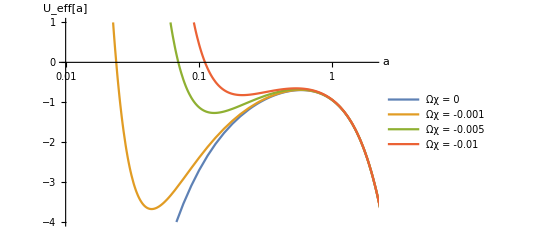

```mathematica
LogLinearPlot[{-Ωm/a-ΩΛ a^2-0/a^2.5,-Ωm/a-ΩΛ a^2+0.001/a^2.5,-Ωm/a-ΩΛ a^2+0.005/a^2.5,-Ωm/a-ΩΛ a^2+0.01/a^2.5},{a,0,3},PlotRange->{{0.01,2},{-4,1}},PlotLegends->{"Ωχ = 0","Ωχ = -0.001","Ωχ = -0.005","Ωχ = -0.01"},AxesLabel->{HoldForm[a],HoldForm["U_eff[a]"]},LabelStyle->{FontFamily->"Latin Modern Mono",15,GrayLevel[0]}]
```

```mathematica
s0=NDSolve[{a'[t]==(0.27/a[t]+0.68 a[t]^2-0/a[t]^2.5)^0.5,a'[0]==0},a[t],{t,0,100}]
s1=NDSolve[{a'[t]==(0.27/a[t]+0.68 a[t]^2-0.001/a[t]^2.5)^0.5,a'[0]==0},a[t],{t,0,100}]
```

NDSolve::icordinit: The initial values for all the dependent variables are not explicitly specified. NDSolve will attempt to find consistent initial conditions for all the variables.

NDSolve::icres: NDSolve has computed initial values that give a zero residual for the differential system, but some components are different from those specified. If you need them to be satisfied, giving explicit initial values to all dependent variables is recommended.

{{a[t]→InterpolatingFunction[…][t]}}

NDSolve::icordinit: The initial values for all the dependent variables are not explicitly specified. NDSolve will attempt to find consistent initial conditions for all the variables.

NDSolve::icres: NDSolve has computed initial values that give a zero residual for the differential system, but some components are different from those specified. If you need them to be satisfied, giving explicit initial values to all dependent variables is recommended.

{{a[t]→InterpolatingFunction[…][t]}}

```mathematica
s2=NDSolve[{a'[t]==(0.27/a[t]+0.68 a[t]^2-0.005/a[t]^2.5)^0.5,a'[0]==0},a[t],{t,0,100}]
```

NDSolve::icordinit: The initial values for all the dependent variables are not explicitly specified. NDSolve will attempt to find consistent initial conditions for all the variables.

NDSolve::icres: NDSolve has computed initial values that give a zero residual for the differential system, but some components are different from those specified. If you need them to be satisfied, giving explicit initial values to all dependent variables is recommended.

{{a[t]→InterpolatingFunction[…][t]}}

```mathematica
s3=NDSolve[{a'[t]==(0.27/a[t]+0.68 a[t]^2-0.01/a[t]^2.5)^0.5,a'[0]==0},a[t],{t,0,100}]
```

NDSolve::icordinit: The initial values for all the dependent variables are not explicitly specified. NDSolve will attempt to find consistent initial conditions for all the variables.

NDSolve::icres: NDSolve has computed initial values that give a zero residual for the differential system, but some components are different from those specified. If you need them to be satisfied, giving explicit initial values to all dependent variables is recommended.

{{a[t]→InterpolatingFunction[…][t]}}

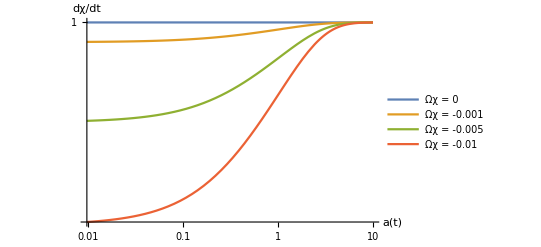

```mathematica
LogLogPlot[Evaluate[{1-0/a[t]/.s0,1-0.001/a[t]/.s1,1-0.005/a[t]/.s2,1-0.01/a[t]/.s3}],{t,0,10},AxesLabel->{HoldForm[a[t]],HoldForm["dχ/dt"]},PlotLegends->{"Ωχ = 0","Ωχ = -0.001","Ωχ = -0.005","Ωχ = -0.01"},LabelStyle->{FontFamily->"Latin Modern Mono",15,GrayLevel[0]}]
```

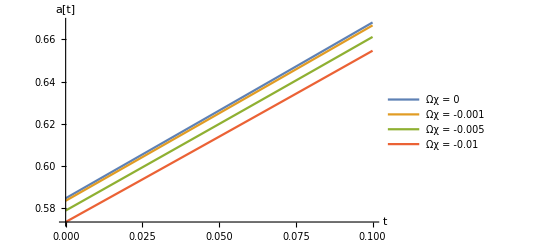

```mathematica
Plot[Evaluate[{a[t]/.s0,a[t]/.s1,a[t]/.s2,a[t]/.s3}],{t,0,0.1},AxesLabel->{HoldForm[t],HoldForm["a[t]"]},PlotLegends->{"Ωχ = 0","Ωχ = -0.001","Ωχ = -0.005","Ωχ = -0.01"},LabelStyle->{FontFamily->"Latin Modern Mono",15,GrayLevel[0]}]
```

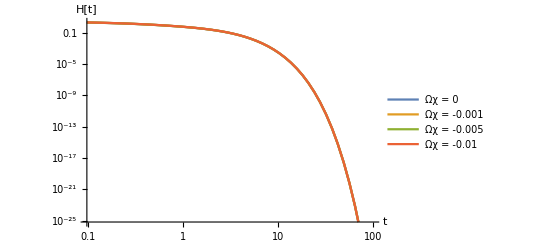

```mathematica
LogLogPlot[Evaluate[{1/a[t]^2(0.27/a[t]+0.68 a[t]^2-0/a[t]^2.5)^0.5/.s0,1/a[t]^2(0.27/a[t]+0.68 a[t]^2-0.001/a[t]^2.5)^0.5/.s1,1/a[t]^2(0.27/a[t]+0.68 a[t]^2-0.005/a[t]^2.5)^0.5/.s2,1/a[t]^2(0.27/a[t]+0.68 a[t]^2-0.01/a[t]^2.5)^0.5/.s3}],{t,0,100},AxesLabel->{HoldForm[t],HoldForm["H[t]"]},PlotLegends->{"Ωχ = 0","Ωχ = -0.001","Ωχ = -0.005","Ωχ = -0.01"},LabelStyle->{FontFamily->"Latin Modern Mono",15,GrayLevel[0]}]
```